```mathematica
B=Import["/home/gutiloluis/gillespie/b.dat"];
Kr=Import["/home/gutiloluis/gillespie/kr.dat"];
Taup=Import["/home/gutiloluis/gillespie/taup.dat"];
```

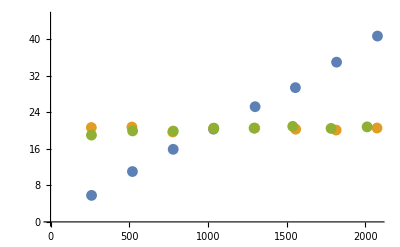

```mathematica
p1=ListPlot[{B,Kr,Taup},PlotRange->{0,45}]
```

```mathematica
kr := 0.01;
taur:=120 ;
taup:=3600 ;
gr:=Log[2]/taur;
gp:=Log[2]/taup;
b:=20;
kp:=b*g_r;
```

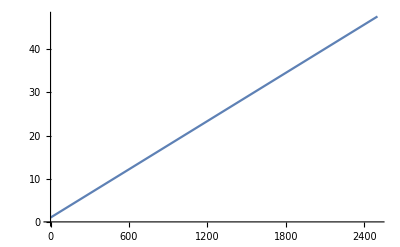

```mathematica
Plot[(gp/kr)*x/(1+gp/gr)+1,{x,0,2500}]
```

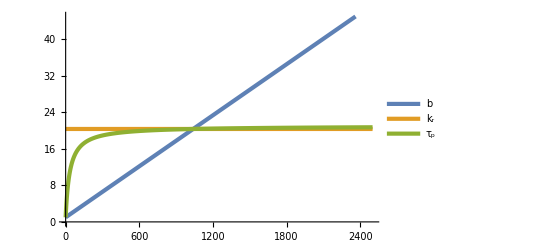

```mathematica
p2=Plot[{(gp/kr)*x/(1+gp/gr)+1,b/(1+gp/gr)+1,b/(1+kr*b/(gr*x))+1},{x,0,2500},PlotRange->{0,45},PlotStyle->AbsoluteThickness[3],PlotLegends->Placed[LineLegend[{"b","k_r","τ_p"},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",35},LegendLayout->{"Row",3},Spacings->0.2],{0.88,0.2}]]
```

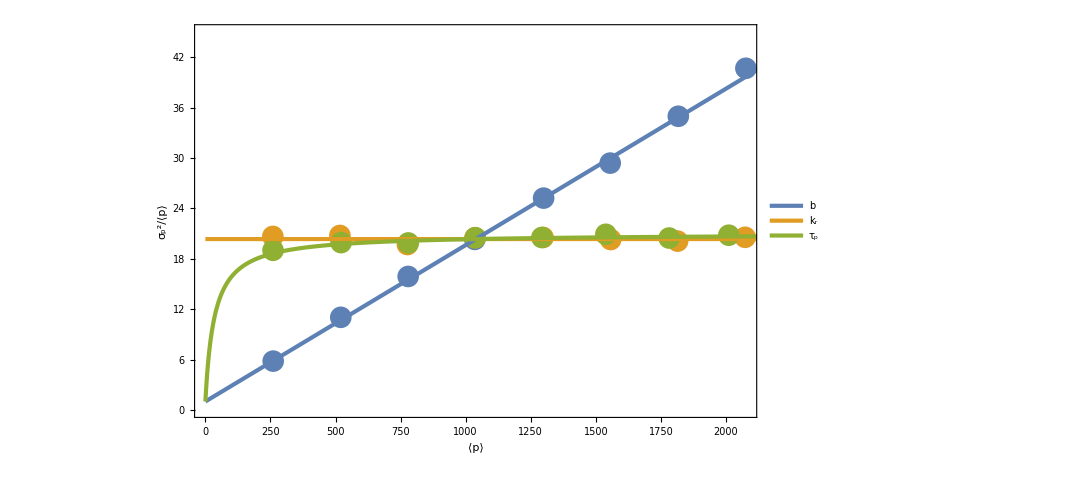

```mathematica
Show[p1,p2,ImageSize->800,Frame->True,FrameStyle->Black,FrameLabel->{Text[Style[ToExpression["\\langle p\\rangle",TeXForm,HoldForm],Large]],Text[Style[ToExpression["\\frac{\\sigma_p^2}{\\langle p\\rangle}",TeXForm,HoldForm],30]]},RotateLabel->False,LabelStyle->Directive[18,FontFamily->"Palatino Linotype",Black]]
```

```mathematica
NN=Import["/home/gutiloluis/61Monograph/gillespie/n.dat"];
KD=Import["/home/gutiloluis/61Monograph/gillespie/Kd.dat"];
```

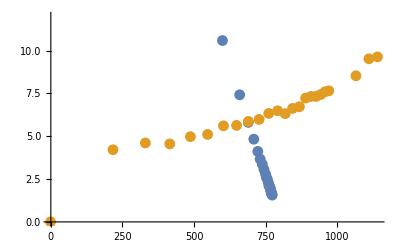

```mathematica
p3=ListPlot[{NN,KD},PlotRange->{0,12}]
```

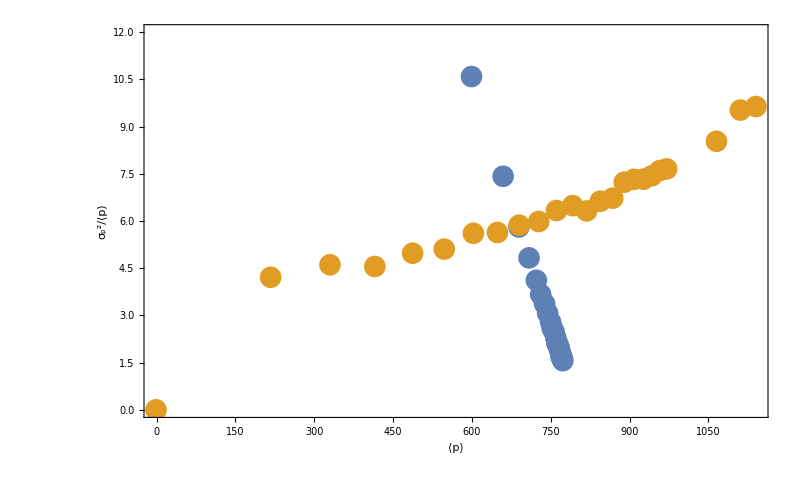

```mathematica
Show[p3,ImageSize->800,Frame->True,FrameStyle->Black,FrameLabel->{Text[Style[ToExpression["\\langle p\\rangle",TeXForm,HoldForm],Large]],Text[Style[ToExpression["\\frac{\\sigma_p^2}{\\langle p\\rangle}",TeXForm,HoldForm],30]]},RotateLabel->False,LabelStyle->Directive[18,FontFamily->"Palatino Linotype",Black]]
```